## CarPark Problem: Simple Replicator with Pure Strategies

```mathematica
parameters = {d1->20,d2->2,α->1,β->5};
```

```mathematica
payoff[x_,y_] := 
(* x going to carpark A, y going to carpark B *)
(* returns tuple with payoff per individual (carpark A, carpark B)  *)
{1/(d1+α x), 1/(d2 + β y)}/. parameters
```

We are playing an n-Player game. Make sure that the population is much larger than n.

```mathematica
populationSize=100;
```

```mathematica
gameSize=10;
```

```mathematica
payoffSingleGame[indexList_]:= 
Module[{traitValues=population[[indexList]], visitorsA, visitorsB},
{visitorsA,visitorsB}=Table[Count[traitValues,i],{i,1,2}];
payoffs=payoff[visitorsA, visitorsB];
Map[payoffs[[#]]&,traitValues]
]
```

```mathematica
oneRound[]:=
Module[{allGames, traitsInGameOrder, payoffsInGameOrder},
allGames=Partition[RandomSample[Range[populationSize]],gameSize];
traitsInGameOrder=population[[allGames//Flatten]];
payoffsInGameOrder=Map[payoffSingleGame,allGames]//Flatten;
population=RandomChoice[payoffsInGameOrder->traitsInGameOrder,populationSize]
]
```

```mathematica
play[tEnd_, plotInterval_]:=
Module[{},
population = RandomChoice[{0.01,0.99}->{1,2}, populationSize];
For[t=1,t≤tEnd,t++,
If[Mod[t,plotInterval]==0,Sow[{{t,Count[population,1]}}]];
oneRound[]
]
]
```

```mathematica
plotEvolution[tEnd_, plotInterval_] := 
(data=Flatten[Reap[play[tEnd, plotInterval]][[2]],2];
Print[ListPlot[data,PlotRange->{0,populationSize}]]
)
```

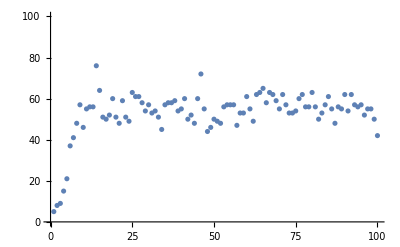

{0.053828,Null}

```mathematica
Timing[plotEvolution[100,1]]
```

Play with gamesizes 10,20. What do you observe for the payoff at both carparks in steady-state. Does this agree with your expectations? Explain the reasons for your reasoning.

The fractions do not actually steady into a steady state but fluctuate around it instead. You need large population sizes (n>1,000) and should use sufficiently long simulation horizons (t=1,000) to see easily interpretable reasonable results.

Payoff should be equal for both carparks. The exact steady-state solution for our current games size (10) is:

```mathematica
Solve[x+y==gameSize&&(1/(d1+α x)== 1/(d2 + β y))/. parameters,{x,y}]
```

{{x→16/3,y→14/3}}

```mathematica
%//N
```

{{x→5.33333,y→4.66667}}

but this can't be achieved since we are dealing with discrete (integer) populations. So no game can ever settle on exactly equal payoff . For example, for game size 10, we have:

```mathematica
payoff[5,5]
```

{1/25,1/27}

```mathematica
payoff[6,4]
```

{1/26,1/22}

```mathematica
payoff[4,6]
```

{1/24,1/32}